```mathematica
u090494e　荒井直幸　2014年12月2日
```

```mathematica
Random[]
RandomReal[]
RandomInteger[]
```

0.0172544

0.329697

0

```mathematica
RandomReal[{0,100}]
RandomInteger[{0,100}]
```

9.02068

78

```mathematica
i=0;
While[i≤9,Print[RandomReal[{0,10}]];i++]
```

8.98439

9.04742

8.75292

6.7798

7.70693

2.30415

8.58847

2.24643

2.58303

6.53243

```mathematica
i=0;
atari=0;
While[i≤4,no1=RandomInteger[{0,30}];no2=RandomInteger[{0,30}];ans=no1+no2;Print[no1,"足す",no2,"は？"];you=Input[];If[you==ans,{Print["あなた＝",you,"　正解！"];atari++},Print["あなた＝",you,"　はずれ！","　答えは",ans"です。"]];Print[" "];i++]
Print["ゲーム終了です。"]
Print[N[atari*20],"です。"]
```

14足す9は？

あなた＝1　はずれ！　答えは23 です。

27足す27は？

あなた＝54　正解！

9足す20は？

あなた＝29　正解！

26足す26は？

あなた＝52　正解！

13足す24は？

あなた＝37　正解！

ゲーム終了です。

80.です。

```mathematica
課題１
```

```mathematica
i=0;
atari=0;
While[i≤4,no3=RandomInteger[{0,30}];no4=RandomInteger[{0,30}];ans1=no3+no4;ans2=no3-no4;
random=If[RandomInteger[{0,1}]==0,ans1,ans2];If[random==ans1,Print[no3,"足す",no4,"は？"],Print[no3,"引く",no4,"は？"]];you=Input[];If[you==random,{Print["あなた＝",you,"　正解！"];atari++},Print["あなた＝",you,"　はずれ！","　答えは",ans"です。"]];Print[" "];i++]
Print["ゲーム終了です。"]
Print[N[atari*20],"です。"]
```

2足す26は？

あなた＝28　正解！

20引く2は？

あなた＝18　正解！

19引く30は？

あなた＝-11　正解！

10引く2は？

あなた＝8　正解！

25足す16は？

あなた＝41　正解！

ゲーム終了です。

100.です。

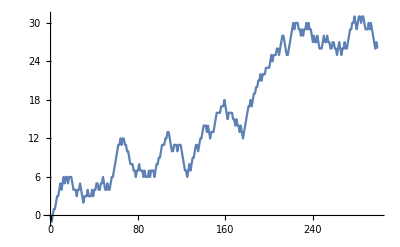

```mathematica
rwalk={};x=0;y=0;i=0;While[i<300,x=i;y=y+RandomInteger[{-1,1}];AppendTo[rwalk,{x,y}];i++]
ListPlot[rwalk,Joined->True]
```

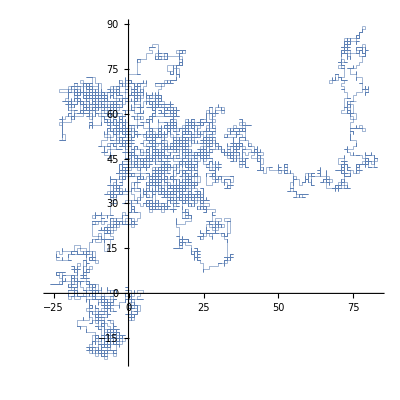

```mathematica
rwalk2={};x=0;y=0;i=0;While[i<10000,rand=RandomInteger[{1,4}];Which[rand==1,x=x+1,rand==2,x=x-1,rand==3,y=y+1,rand==4,y=y-1];AppendTo[rwalk2,{x,y}];i++]
ListPlot[rwalk2,Joined->True,PlotStyle->{Thickness[0.001]},AspectRatio->1]
```

```mathematica
rwalk3={};x=0;y=0;z=0;i=0;While[i<10000,rand=RandomInteger[{1,6}];Which[rand==1,x=x+1,rand==2,x=x-1,rand==3,y=y+1,rand==4,y=y-1,rand==5,z=z+1,rand==6,z=z-1];AppendTo[rwalk3,{x,y,z}];i++]
Graphics3D[{Red,Line[rwalk3]}]
```

-Graphics3D-

```mathematica
課題２
```

```mathematica
rwalk4={};x=0;y=0;z=0;i=0;While[i<10000,kakudo1=RandomReal[{0,2 Pi}];kakudo2=RandomReal[{0,Pi}];x=x+Cos[kakudo1] Sin[kakudo2];y=y+Sin[kakudo1] Sin[kakudo2];z=z+Cos[kakudo2];AppendTo[rwalk4,{x,y,z}];i++]
Graphics3D[{Red,Line[rwalk4]}]
```

-Graphics3D-